```mathematica
f[x_]:=Sin[x]
range={-2*Pi,2*Pi,0.01};
```

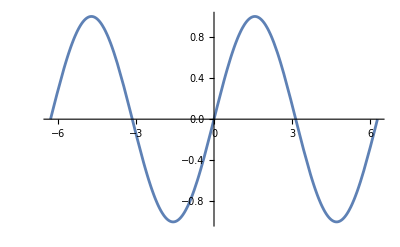

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
(* pRange[[2,1]]=Min[0,pRange[[2,1]]]; *)(* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

## Helper Functions

As many operations in this notebook take a very long time to run, this function gives an progress indicator for them:

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[
{originalTime=AbsoluteTime[],progress=PrintTemporary["0% "<>message], timeUsed},
timeUsed:=AbsoluteTime[]-originalTime;
Table[NotebookDelete[progress];
progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message<>" (ETA: "<>DateString[AbsoluteTime[]+Round[(timeUsed/i)*(Length[l]-i)]]<>")"];
func[l[[i]]],{i, Length[l]}]]
```

Makes a linear spline between points (i.e. connects them with straight lines), and extends the domain using the last two points on either end.

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

squared difference error:

```mathematica
error[af_]:=Quiet[Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}],General::munfl]
```

```mathematica
realToComplexPlot[func_, range__]:=Plot[Abs[func], range, ColorFunction->Function[{xx, z},Hue[(N[Arg[func/.range[[1]]->xx]/Pi])+.5]]]
realToComplexPlot[E^(I*Pi*x), {x, -3, 3}]
```

-Graphics-

## Original Method

```mathematica
doRecompute=False;
```

```mathematica
aFunc= 0&;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

(* Generates the interpolating function from a list of y values *)
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

$Aborted

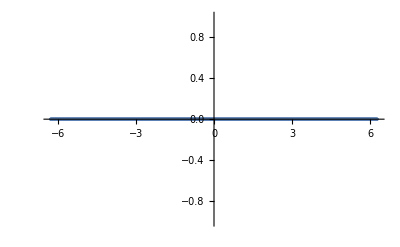

```mathematica
PlotVals[vals_, options___]:=Show[{ListPlot[Transpose[{xVals, vals}], Join[{options},{PlotRange->pRange}]], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

```mathematica
precomputedValue=If[precomputedValue[[0]]===Symbol,, precomputedValue];
doRecompute=If[Length[precomputedValue]==Length[xVals],!(doRecompute===True||doRecompute===False),True];
Button["Recompute", doRecompute=True]
Dynamic[doRecompute]
```

Recompute

```mathematica
aValsHist=If[doRecompute,{aVals}, {precomputedValue}];
If[doRecompute,progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[500] , "Optimized"]];
```

```mathematica
Iconize[aVals]
```

```mathematica
(* Find the optimization which actually minimized error *)
precomputedValue=bestVals=If[doRecompute,aValsHist[[First[PositionSmallest[eHist=ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]], precomputedValue];
doRecompute=False;
```

```mathematica
aFunc=funcFromVals[bestVals];
```

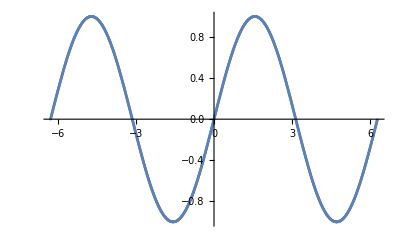

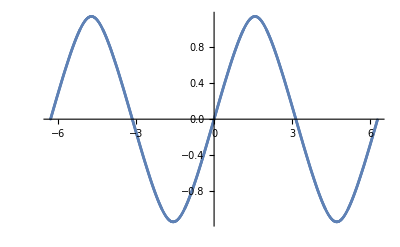

```mathematica
PlotVals[fVals]
PlotVals[bestVals, PlotRange->Automatic]
```

```mathematica
eBest=error[aFunc]
```

3.80825×10^-29

## Fourier Stuff

```mathematica
four=Fourier[bestVals];
fp=Transpose[{xVals,four}];
```

For removing outliers:

15

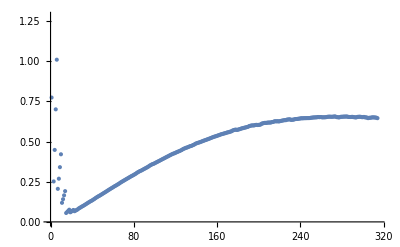

```mathematica
generateFPC[clipAmount_]:=fp[[1+clipAmount;;-clipAmount]];
stdDevByC=(StandardDeviation[Abs/@generateFPC[#][[All, 2]]]*(#^2))&/@Range[Round[Length[four]/4]];
clipAmount=First[PositionSmallest[stdDevByC]]
ListPlot[stdDevByC]
```

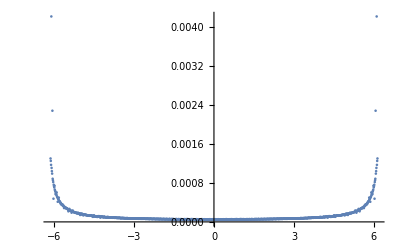

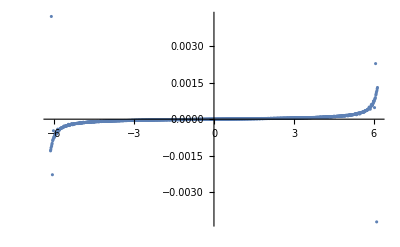

```mathematica
fpc=fp[[1+clipAmount;;-clipAmount]];
fpca={#1, Abs[#2]}&@@@fpc;
fpci={#1, Im[#2]}&@@@fpc;

ListPlot[fpca, PlotRange->All]
ListPlot[fpci, PlotRange->All]
```

### Abs Fit

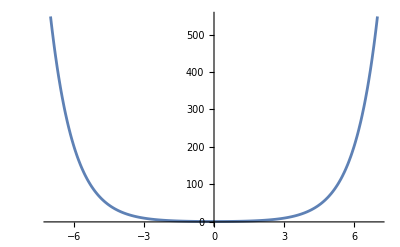

```mathematica
Plot[Cosh[x], {x, -7, 7}]
```

```mathematica
fitAbsSol=FindFit[fpca,a+b Cosh[c x],{a,b,c},x]
fitAbs=a+b Cosh[c x]/.fitAbsSol
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→0.0000699469,b→2.14136×10^-11,c→-3.03107}

0.0000699469+2.14136×10^-11 Cosh[3.03107 x]

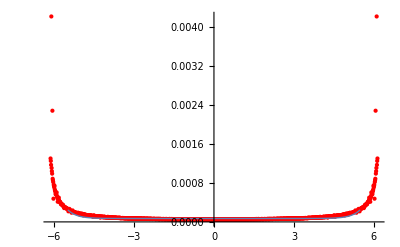

```mathematica
Show[ListPlot[fpca, PlotRange->All, PlotStyle->{Red, PointSize[Small]}], Plot[fitAbs, {x,range[[1]], range[[2]]}, PlotStyle->{Thick}], ImageSize->Full]
```

### Im Fit

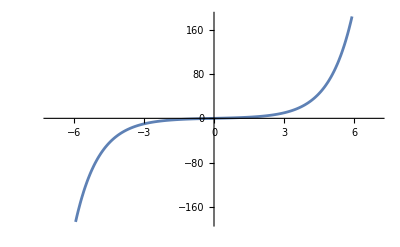

```mathematica
Plot[Sinh[x], {x, -7, 7}]
```

```mathematica
fitImSol=FindFit[fpci,a+b Sinh[c x],{a,b,c},x]
fitIm=a+b Sinh[c x]/.fitImSol
```

{a→-1.99711×10^-7,b→8.18341×10^-7,c→1.20674}

-1.99711×10^-7+8.18341×10^-7 Sinh[1.20674 x]

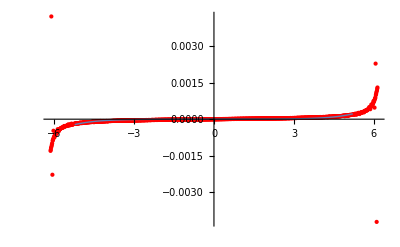

```mathematica
Show[ListPlot[fpci, PlotRange->All, PlotStyle->{Red, PointSize[Small]}], Plot[fitIm, {x,range[[1]], range[[2]]}, PlotStyle->{Thick}], ImageSize->Full]
```

#### FitAll

```mathematica
fitAllF[y_]:=(I fitIm -Sqrt[fitAbs^2 -fitIm^2]/.x->y)
```

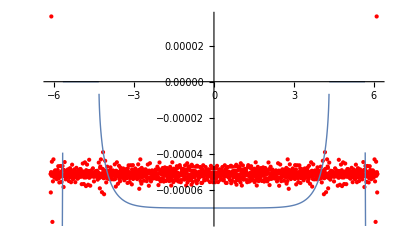

```mathematica
Show[ListPlot[Re/@fpc, PlotRange->All, PlotStyle->{Red, PointSize[Small]}], Plot[Re[fitAllF[x]], {x,range[[1]], range[[2]]}, PlotStyle->{Thick}], ImageSize->Full]
```

```mathematica
allPointsFourier=fitAllF/@xVals;
```

```mathematica
allPoints=InverseFourier[allPointsFourier];
```

```mathematica
all=Transpose[{xVals, Re/@allPoints}];
alFunc=funcFromVals[Re/@allPoints];
```

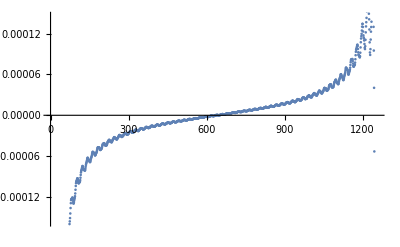

```mathematica
ListPlot[Re/@allPoints]
```

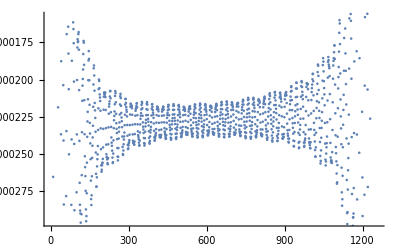

```mathematica
ListPlot[Im/@allPoints]
```

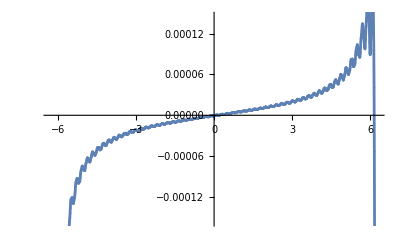

```mathematica
Show[ListPlot[all], Plot[alFunc[x], {x, range[[1]], range[[2]]}, PlotRange->All]]
```

```mathematica
error[alFunc]
```

628.319

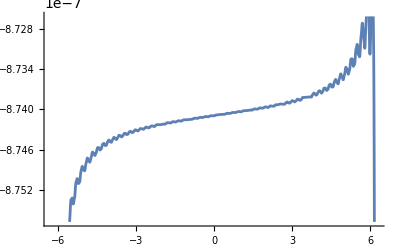

```mathematica
Plot[alFunc[alFunc[x]], {x, range[[1]], range[[2]]}]
```